```mathematica
a={3,3,-4,1};
b={5,3,-4,1};
c={5,5,-4,1};
d={3,5,-4,1};
aPrime={3,3,-6,1};
bPrime={5,3,-6,1};
cPrime={5,5,-6,1};
dPrime={3,5,-6,1};
d2Prime={8,8,-6,1};
Oc={0,0,0,1};
zeta1 = 1;
zeta2=1;
alpha=45;
beta = 0;
Oc2={6,0,3,1};
Rot2=RotationsE2[alpha];
Rot1=RotationsE2[beta];
ObjectSize = b[[1]]-a[[1]];
A={{2.5,0,0,0},{0,6.3,0,0},{0,0,1,0},{0,0,0,1}};
AK={{2.5,0,0},{0,6.3,0},{0,0,1}};
```

```mathematica
ClearAll["Global`*"];
```

PM1 = {{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,1,0}}

PM2 = {{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,1,0}}

PM2 = {{2.5,0.,0.,0.},{0.,6.3,0.,0.},{0.,0.,1.,0.},{0.,0.,1.,0.}}

OC2 = {6,0,3,1}

M of C2=(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

M2 of C1 =(1/(√2) | 0 | -1/(√2) | -3/(√2)
0 | 1 | 0 | 0
1/(√2) | 0 | 1/(√2) | -9/(√2)
0 | 0 | 0 | 1)

ProjectionMtxCamera1(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 1 | 0)

ProjectionMtxCamera2(1.76777 | 0. | -1.76777 | -5.3033
0. | 6.3 | 0. | 0.
0.707107 | 0. | 0.707107 | -6.36396
0.707107 | 0. | 0.707107 | -6.36396)

CameraProjectedPointsK1 = (3 | 3 | -4 | -4
5 | 3 | -4 | -4
5 | 5 | -4 | -4
3 | 5 | -4 | -4
3 | 3 | -6 | -6
5 | 3 | -6 | -6
5 | 5 | -6 | -6
3 | 5 | -6 | -6
8 | 8 | -6 | -6)

CameraProjectedPointsK2 = (7.07107 | 18.9 | -7.07107 | -7.07107
10.6066 | 18.9 | -5.65685 | -5.65685
10.6066 | 31.5 | -5.65685 | -5.65685
7.07107 | 31.5 | -7.07107 | -7.07107
10.6066 | 18.9 | -8.48528 | -8.48528
14.1421 | 18.9 | -7.07107 | -7.07107
14.1421 | 31.5 | -7.07107 | -7.07107
10.6066 | 31.5 | -8.48528 | -8.48528
19.4454 | 50.4 | -4.94975 | -4.94975)

homogene CameraProjectedPointsK1 = (-3/4 | -3/4 | 1 | 1
-5/4 | -3/4 | 1 | 1
-5/4 | -5/4 | 1 | 1
-3/4 | -5/4 | 1 | 1
-1/2 | -1/2 | 1 | 1
-5/6 | -1/2 | 1 | 1
-5/6 | -5/6 | 1 | 1
-1/2 | -5/6 | 1 | 1
-4/3 | -4/3 | 1 | 1)

homogene CameraProjectedPointsK2 = (-1. | -2.67286 | 1. | 1.
-1.875 | -3.34108 | 1. | 1.
-1.875 | -5.56847 | 1. | 1.
-1. | -4.45477 | 1. | 1.
-1.25 | -2.22739 | 1. | 1.
-2. | -2.67286 | 1. | 1.
-2. | -4.45477 | 1. | 1.
-1.25 | -3.71231 | 1. | 1.
-3.92857 | -10.1823 | 1. | 1.)

Begin construct Epipol_______________________________________________

End construct Epipol_______________________________________________

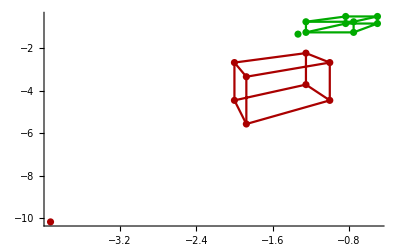

ImagePlaneC1Points = (-3/4 | -3/4 | 1
-5/4 | -3/4 | 1
-5/4 | -5/4 | 1
-3/4 | -5/4 | 1
-1/2 | -1/2 | 1
-5/6 | -1/2 | 1
-5/6 | -5/6 | 1
-1/2 | -5/6 | 1
-4/3 | -4/3 | 1)

ImagePlaneC2Points = (-1. | -2.67286 | 1.
-1.875 | -3.34108 | 1.
-1.875 | -5.56847 | 1.
-1. | -4.45477 | 1.
-1.25 | -2.22739 | 1.
-2. | -2.67286 | 1.
-2. | -4.45477 | 1.
-1.25 | -3.71231 | 1.
-3.92857 | -10.1823 | 1.)

CoefficientMtx = (0.75 | 0.75 | -1. | 2.00465 | 2.00465 | -2.67286 | -3/4 | -3/4 | 1
2.34375 | 1.40625 | -1.875 | 4.17635 | 2.50581 | -3.34108 | -5/4 | -3/4 | 1
2.34375 | 2.34375 | -1.875 | 6.96058 | 6.96058 | -5.56847 | -5/4 | -5/4 | 1
0.75 | 1.25 | -1. | 3.34108 | 5.56847 | -4.45477 | -3/4 | -5/4 | 1
0.625 | 0.625 | -1.25 | 1.11369 | 1.11369 | -2.22739 | -1/2 | -1/2 | 1
1.66667 | 1. | -2. | 2.22739 | 1.33643 | -2.67286 | -5/6 | -1/2 | 1
1.66667 | 1.66667 | -2. | 3.71231 | 3.71231 | -4.45477 | -5/6 | -5/6 | 1
0.625 | 1.04167 | -1.25 | 1.85616 | 3.09359 | -3.71231 | -1/2 | -5/6 | 1
5.2381 | 5.2381 | -3.92857 | 13.5765 | 13.5765 | -10.1823 | -4/3 | -4/3 | 1)

RowReduce CoefficientMtx = [(1 | 0. | 0. | 0. | 0. | 0. | 0. | 2.6446×10^-15 | 0.
0 | 1 | 0. | 0. | 0. | 0. | 0. | 1.2 | 0.
0 | 0 | 1 | 0. | 0. | 0. | 0. | -2.64233×10^-15 | 0.
0 | 0 | 0 | 1 | 0. | 0. | 0. | -0.224478 | 0.
0 | 0 | 0 | 0 | 1 | 0. | 0. | -2.74477×10^-15 | 0.
0 | 0 | 0 | 0 | 0 | 1 | 0. | 0.448957 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1.84297×10^-14 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)]

ns ={{-2.40249×10^-15,0.731388,-3.78555×10^-16,-0.136817,1.03249×10^-15,0.273634,-7.53159×10^-15,-0.60949,-5.23502×10^-16}}

F = (-2.40249×10^-15 | 0.731388 | -3.78555×10^-16
-0.136817 | 1.03249×10^-15 | 0.273634
-7.53159×10^-15 | -0.60949 | -5.23502×10^-16)

lC1 = {{-0.548541,0.376247,0.457117},{-0.548541,0.444656,0.457117},{-0.914234,0.444656,0.761862},{-0.914234,0.376247,0.761862},{-0.365694,0.342043,0.304745},{-0.365694,0.387649,0.304745},{-0.60949,0.387649,0.507908},{-0.60949,0.342043,0.507908},{-0.975183,0.456057,0.812653}}

lPrimeC1 = {{0.365694,-1.34088,-0.731388},{0.457117,-1.98084,-0.914234},{0.761862,-1.98084,-1.52372},{0.60949,-1.34088,-1.21898},{0.304745,-1.52372,-0.60949},{0.365694,-2.07226,-0.731388},{0.60949,-2.07226,-1.21898},{0.507908,-1.52372,-1.01582},{1.39312,-3.4828,-2.78624}}

e = {0.894427,-2.77556×10^-15,0.447214}

e' = {-0.640184,9.21485×10^-15,-0.768221}

EpipoleLines = (-1.2 | 0.823087 | 1.
-1.2 | 0.972739 | 1.
-1.2 | 0.583644 | 1.
-1.2 | 0.493852 | 1.
-1.2 | 1.12239 | 1.
-1.2 | 1.27204 | 1.
-1.2 | 0.763226 | 1.
-1.2 | 0.673435 | 1.
-1.2 | 0.561196 | 1.)

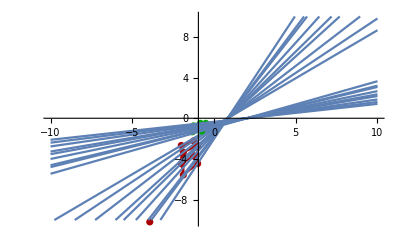

Begin Computing essential Matrix___________________________________________________

EMtx = {{-6.00622×10^-15,1.82847,-9.46386×10^-16},{-0.861948,6.50469×10^-15,1.7239},{-7.53159×10^-15,-0.60949,-5.23502×10^-16}}

U of E = {{-3.67091×10^-15,0.948683,-0.316228},{1.,4.44089×10^-15,1.66533×10^-15},{2.9976×10^-15,-0.316228,-0.948683}}

Sigma of E = {{1.92738,0.,0.},{0.,1.92738,0.},{0.,0.,0.}}

V of E = {{-0.447214,-3.77476×10^-15,0.894427},{-4.94049×10^-15,1.,1.77636×10^-15},{0.894427,3.59915×10^-15,0.447214}}

S1 = (0. | 0.948683 | 1.68293×10^-15
-0.948683 | 0. | 0.316228
-1.68293×10^-15 | -0.316228 | 0.)

S2 = (0. | -0.948683 | -1.68293×10^-15
0.948683 | 0. | -0.316228
1.68293×10^-15 | 0.316228 | 0.)

R1 = (0.141421 | 4.54319×10^-16 | -0.989949
-2.9921×10^-16 | 1. | 3.71851×10^-16
-0.989949 | -2.49919×10^-16 | -0.141421)

R2 = (-0.707107 | -1.57779×10^-15 | 0.707107
3.27825×10^-15 | -1. | 1.11767×10^-15
-0.707107 | -3.12048×10^-15 | -0.707107)

Test R1 is rotation ={{1.,1.24469×10^-17,-1.94289×10^-16},{1.24469×10^-17,1.,-4.25574×10^-17},{-1.94289×10^-16,-4.25574×10^-17,1.}}

Test R2 is rotation ={{1.,4.39249×10^-17,-1.11022×10^-16},{4.39249×10^-17,1.,-2.68184×10^-17},{-1.11022×10^-16,-2.68184×10^-17,1.}}

{{0.141421,4.54319×10^-16,-0.989949},{-2.9921×10^-16,1.,3.71851×10^-16},{-0.989949,-2.49919×10^-16,-0.141421}} is no Rotation

{{-0.707107,-1.57779×10^-15,0.707107},{3.27825×10^-15,-1.,1.11767×10^-15},{-0.707107,-3.12048×10^-15,-0.707107}} is no Rotation

Check if t of S1, S2 is equal = {{{0.316228,-1.66533×10^-15,0.948683}},{{0.316228,-1.66533×10^-15,0.948683}}}

t = {0.316228,-1.66533×10^-15,0.948683}

P21  = (-0.707107 | -1.57779×10^-15 | 0.707107 | -0.316228
3.27825×10^-15 | -1. | 1.11767×10^-15 | 1.66533×10^-15
-0.707107 | -3.12048×10^-15 | -0.707107 | -0.948683)

P22  = (0.141421 | 4.54319×10^-16 | -0.989949 | -0.316228
-2.9921×10^-16 | 1. | 3.71851×10^-16 | 1.66533×10^-15
-0.989949 | -2.49919×10^-16 | -0.141421 | -0.948683)

P23  = (-0.707107 | -1.57779×10^-15 | 0.707107 | 0.316228
3.27825×10^-15 | -1. | 1.11767×10^-15 | -1.66533×10^-15
-0.707107 | -3.12048×10^-15 | -0.707107 | 0.948683)

P24  = (0.141421 | 4.54319×10^-16 | -0.989949 | 0.316228
-2.9921×10^-16 | 1. | 3.71851×10^-16 | -1.66533×10^-15
-0.989949 | -2.49919×10^-16 | -0.141421 | 0.948683)

End Computing essential Matrix___________________________________________________

```mathematica
StartComputation[];
```